Solution 1: Solve just with calculator... Solution 2:

```mathematica
a = Abs[(-1+Sqrt[-31])/2]
```

2 √2

```mathematica
s = (-1+Sqrt[-31])/2
P = FullSimplify[{Re[s],Im[s]}]
```

1/2 (-1+ⅈ √31)

{-1/2,(√31)/2}

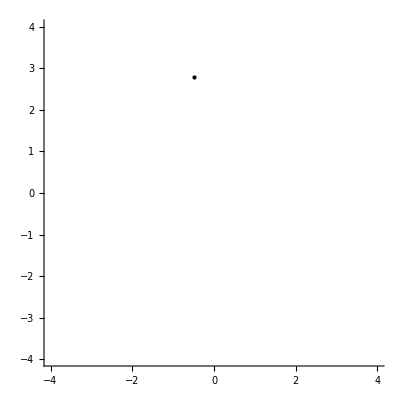

```mathematica
CmplxPlane1=ListPlot[{P},PlotRange->{{-4,4},{-4,4}}, AspectRatio->1,PlotStyle->{Black,PointSize[Large]}]
```

```mathematica
Export["CmplxPlane1.pdf",CmplxPlane1]
```

CmplxPlane1.pdf

```mathematica
Q=  FullSimplify[{Re[s]/a,Im[s]/a}];
```

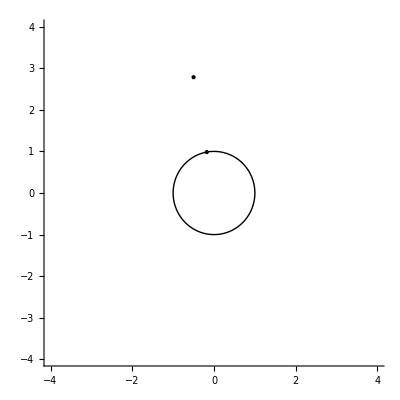

```mathematica
CmplxPlane2Q=ListPlot[{Q},PlotRange->{{-4,4},{-4,4}}, AspectRatio->1,PlotStyle->{Black,PointSize[Large]}];
circle = ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi},PlotStyle->Black];
CmplxPlane2 =Show[CmplxPlane1,CmplxPlane2Q,circle]
```

```mathematica
Export["CmplxPlane2.pdf",CmplxPlane2]
```

CmplxPlane2.pdf

{√2 Cos[1/3 ArcSin[(√(31/2))/4]],√2 Sin[1/3 ArcSin[(√(31/2))/4]]}

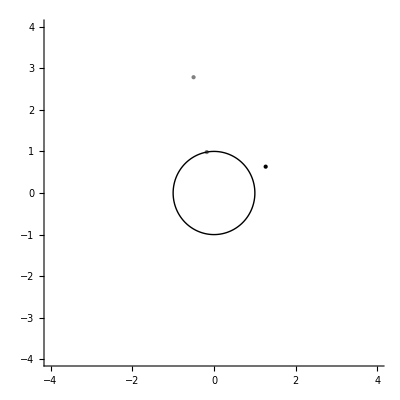

```mathematica
R = a^(1/3) {Cos[ArcCos[Q[[1]]]/3],Sin[ArcCos[Q[[1]]]/3]};
R = a^(1/3) {Cos[ArcSin[Q[[2]]]/3],Sin[ArcSin[Q[[2]]]/3]}
CmplxPlane1=ListPlot[{P},PlotRange->{{-4,4},{-4,4}}, AspectRatio->1,PlotStyle->{Gray,PointSize[Large]}];
CmplxPlane2Q=ListPlot[{Q},PlotRange->{{-4,4},{-4,4}}, AspectRatio->1,PlotStyle->{Gray,PointSize[Large]}];
CmplxPlane3R=ListPlot[{R},PlotRange->{{-4,4},{-4,4}}, AspectRatio->1,PlotStyle->{Black,PointSize[Large]}];
circle = ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi},PlotStyle->Black];
CmplxPlane3 =Show[CmplxPlane1,CmplxPlane2Q,CmplxPlane3R,circle]
```

```mathematica
Export["CmplxPlane3.pdf",CmplxPlane3]
```

CmplxPlane3.pdf

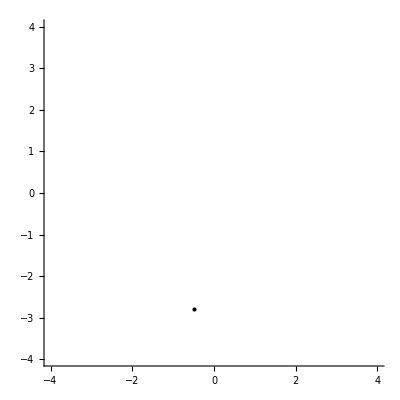

```mathematica
ss = 8/s;
PP = {Re[ss],Im[ss]};
CmplxPlane4=ListPlot[{PP},PlotRange->{{-4,4},{-4,4}}, AspectRatio->1,PlotStyle->{Black,PointSize[Large]}]
```

```mathematica
Export["CmplxPlane4.pdf",CmplxPlane4]
```

CmplxPlane4.pdf

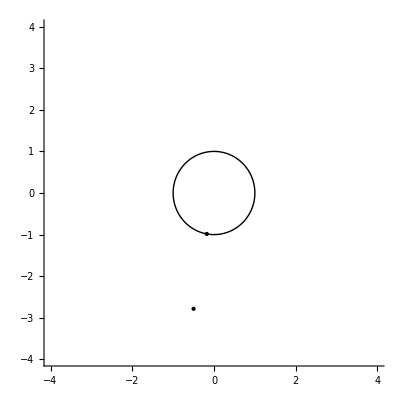

```mathematica
QQ=  FullSimplify[{Re[ss]/a,Im[ss]/a}];
CmplxPlane5Q=ListPlot[{QQ},PlotRange->{{-4,4},{-4,4}}, AspectRatio->1,PlotStyle->{Black,PointSize[Large]}];
circle = ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi},PlotStyle->Black];
CmplxPlane5 =Show[CmplxPlane4,CmplxPlane5Q,circle]
```

```mathematica
Export["CmplxPlane5.pdf",CmplxPlane5]
```

CmplxPlane5.pdf

{√2 Cos[1/3 ArcSin[(√(31/2))/4]],-√2 Sin[1/3 ArcSin[(√(31/2))/4]]}

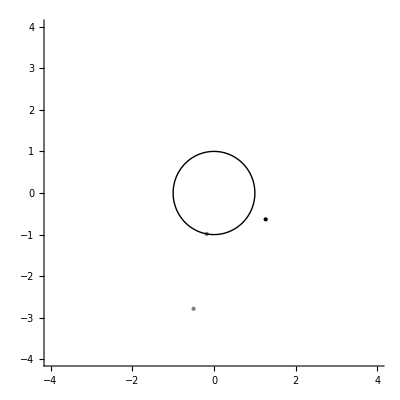

```mathematica
RR = a^(1/3) {Cos[ArcCos[QQ[[1]]]/3],Sin[ArcCos[QQ[[1]]]/3]};
RR = a^(1/3) {Cos[ArcSin[QQ[[2]]]/3],Sin[ArcSin[QQ[[2]]]/3]}
CmplxPlane4=ListPlot[{PP},PlotRange->{{-4,4},{-4,4}}, AspectRatio->1,PlotStyle->{Gray,PointSize[Large]}];
CmplxPlane5Q=ListPlot[{QQ},PlotRange->{{-4,4},{-4,4}}, AspectRatio->1,PlotStyle->{Gray,PointSize[Large]}];
CmplxPlane6R=ListPlot[{RR},PlotRange->{{-4,4},{-4,4}}, AspectRatio->1,PlotStyle->{Black,PointSize[Large]}];
circle = ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi},PlotStyle->Black];
CmplxPlane6 =Show[CmplxPlane4,CmplxPlane5Q,CmplxPlane6R,circle]
```

```mathematica
Export["CmplxPlane6.pdf",CmplxPlane6]
```

CmplxPlane6.pdf

```mathematica
Simplify[(c-d)^(1/3) + (c+d)^(1/3)]
```

(c-d)^(1/3)+(c+d)^(1/3)